```mathematica
Remove["Global`*"]
```

## Setting things up

We manually define the Weyl group for G2. It has generators s1,s2 which act by left multiplication by the letter 1,2 respectively. The relations are s1^2=s2^2=1 and (s1 s2)^6=1. The inverse of a word is just its reverse. 
We define T=⟨w s_i w^-1 | w ∈ W⟩. We build a graph with arrows w→tw if the reduced word tw is one longer than w. In principle we could easily compute this in Mathematica, but in stead we computed this by hand and input this graph manually.

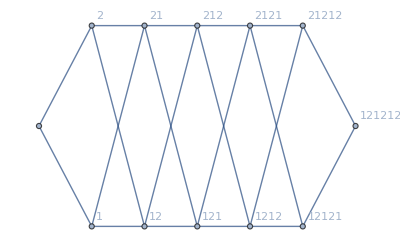

```mathematica
W = {"","1","2","12","21","121","212","1212","2121","12121","21212","121212"};
arrows = Select[(#->"1"<>#)&/@W[[;;-2]],StringFreeQ[#[[2]],"11"]&]~Join~Select[(#->"2"<>#)&/@W[[;;-2]],StringFreeQ[#[[2]],"22"]&]~Join~Select[(#->#<>"1")&/@W[[;;-2]],StringFreeQ[#[[2]],"11"]&]~Join~Select[(#->#<>"2")&/@W[[;;-2]],StringFreeQ[#[[2]],"22"]&]/."212121"->"121212"//DeleteDuplicates;

G=UndirectedGraph[arrows,VertexLabels->"Name",GraphLayout->{"MultipartiteEmbedding", "VertexPartition"->{1,2,2,2,2,2,1}}]
```

We define the dot action of the Weyl group W on the root lattice R by w · λ = w(λ+ρ)-ρ, where ρ is the highest weight. R is generated by α_1, α_2, and the action of s_i on a α_1+ b α_2 is given by the functions s[i][{a,b}] below. The function getAction[w,λ] defines the action of a word w∈W by inductively applying the letters s_i of which it consists to the root λ.

```mathematica
s[1][{a_,b_}]:={-a+3b-1,b }
s[2][{a_,b_}]:={a,a-b-1 }
```

```mathematica
getAction[string_,weights_:{0,0}]:=Fold[s[#2][#1]&,weights,ToExpression@Characters[string]]
```

```mathematica
makeRootDisplay[{a_,b_}]:="E["<>ToString[a α1 + b α2]<>"]" (*Helper function to display a root*)
```

We pick a root λ and compute its image under the dot action by all the elements of W and present the result in a graph.

Weights which are good:
{0,0} -- can compute
{2,1} -- can compute

{}

{}

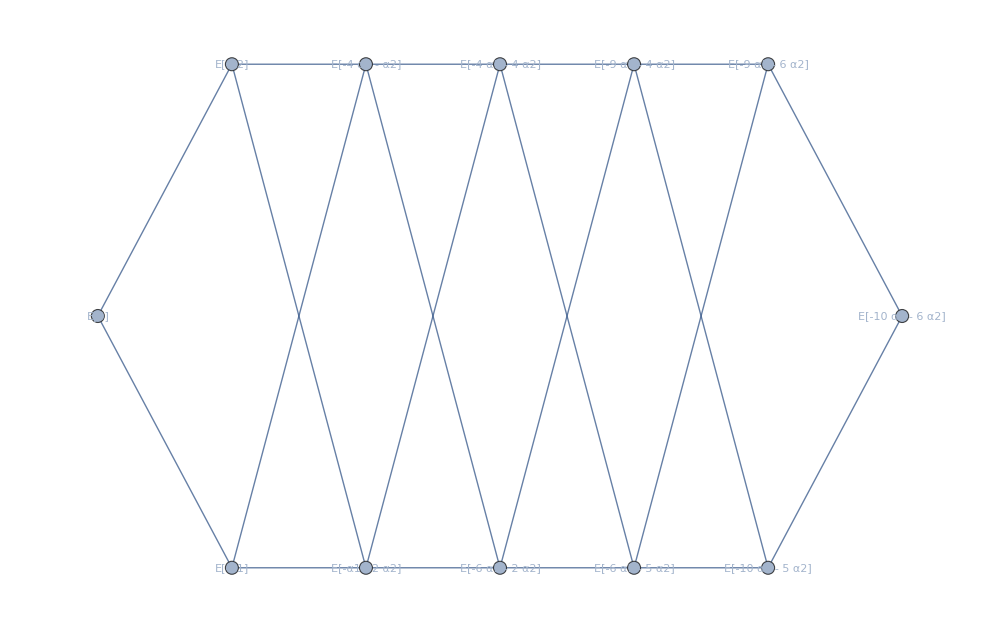

```mathematica
weights = {0,0};
Select[Cases[{EdgeList[G][[#]],getAction[EdgeList[G][[#]][[1]],weights]-getAction[EdgeList[G][[#]][[2]],weights]}&/@Range[EdgeCount[G]],{_,{___,0,___}}],Total[#[[2]]]≤0&](*if this is non-zero, the weight isn't good*)
Select[{EdgeList[G][[#]],getAction[EdgeList[G][[#]][[1]],weights]-getAction[EdgeList[G][[#]][[2]],weights]}&/@Range[EdgeCount[G]],Min[#[[2]]]<0&](*if this is non-zero, the weight isn't good*)
panelLabel[lbl_]:=Panel[lbl,FrameMargins->0,Background->Lighter[Yellow,0.7]]
vertexNames=#->Placed[makeRootDisplay[Simplify[getAction[#,weights]]],Center,panelLabel]&/@W;
Graph[G,VertexLabels->vertexNames,ImageSize->1000]
```

We now want to compute the maps in the BGG complex. A map E[aα_1+b α_2]→E[a' α_1+b' α_2] is necessarily a homogeneous polynomial in noncommutative variables f_1,f_2 of bidegree (a-a', b-b'). Therefore if either a-a’ or b-b’  is 0, then we know the monomial is just f_i^k, but otherwise we do not know. It turns out all the edges on the outside of this graph are of this form. We can then compute the other edges by requiring all admissible cycles to commute. 
A cycle in this graph is admissible if it is of length 4, and its vertices are words of length  l→l+1→l+2→l+1. This just excludes the hourglass-shaped cycles of form l→l+1→l→l+1.

First we find all the admissible cycles.

```mathematica
NormalFormEdge[e_]:=UndirectedEdge@@SortBy[{e[[1]],e[[2]]},StringLength] (*format all the edges such that the first vertex has shorter word length*)
edgeAssoc = Association[NormalFormEdge[EdgeList[G][[#]]]->#&/@Range[EdgeCount[G]]] (*number all the edges*)
edgeAssocReverse = Association[#->NormalFormEdge[EdgeList[G][[#]]]&/@Range[EdgeCount[G]]] 
CycleAllowedQ[c_]:=(Length@DeleteDuplicates@(StringLength/@DeleteDuplicates[Flatten[Table[c[[j,k]],{j,1,4},{k,1,2}]]]))==3
cycles=Map[edgeAssoc@*NormalFormEdge,Select[FindCycle[G,{4},All],CycleAllowedQ],{2}]
```

<|<->1→1,<->2→2,1<->12→3,1<->21→4,2<->12→5,2<->21→6,12<->121→7,12<->212→8,21<->121→9,21<->212→10,121<->1212→11,121<->2121→12,212<->1212→13,212<->2121→14,1212<->12121→15,1212<->21212→16,2121<->12121→17,2121<->21212→18,12121<->121212→19,21212<->121212→20|>

<|1→<->1,2→<->2,3→1<->12,4→1<->21,5→2<->12,6→2<->21,7→12<->121,8→12<->212,9→21<->121,10→21<->212,11→121<->1212,12→121<->2121,13→212<->1212,14→212<->2121,15→1212<->12121,16→1212<->21212,17→2121<->12121,18→2121<->21212,19→12121<->121212,20→21212<->121212|>

{{17,18,20,19},{14,17,15,13},{13,14,18,16},{15,19,20,16},{10,13,11,9},{9,10,14,12},{11,15,17,12},{11,16,18,12},{4,9,7,3},{3,4,10,8},{7,11,13,8},{7,12,14,8},{6,10,8,5},{6,9,7,5},{1,3,5,2},{1,4,6,2}}

We now compute all the maps we can, and store them in a list.

```mathematica
edgeWeights=<||>;
l=Cases[{#,getAction[EdgeList[G][[#]][[1]]]-getAction[EdgeList[G][[#]][[2]]]}&/@Range[EdgeCount[G]],{_,{___,0,___}}];
AssociateTo[edgeWeights,#[[1]]->NonCommutativeMultiply[Subscript[f,FirstPosition[#[[2]], Except[0,_Integer]][[1]]]^Max[Abs[#[[2]]]]]&/@l] (*we store monomials Subscript[f, i]^k as NonCommutativeMultiply[Subscript[f, i]^k]. This is only to make algebraic manipulation with these expressions easier later on.*)
```

<|1→NonCommutativeMultiply[f_1],2→NonCommutativeMultiply[f_2],3→NonCommutativeMultiply[f_2^2],6→NonCommutativeMultiply[f_1^4],7→NonCommutativeMultiply[f_1^5],10→NonCommutativeMultiply[f_2^3],11→NonCommutativeMultiply[f_2^3],14→NonCommutativeMultiply[f_1^5],15→NonCommutativeMultiply[f_1^4],18→NonCommutativeMultiply[f_2^2],19→NonCommutativeMultiply[f_2],20→NonCommutativeMultiply[f_1]|>

## Computing the BGG maps

```mathematica
nonComRels={NonCommutativeMultiply[x___,Plus[y1_+y2_],z___]->NonCommutativeMultiply[x,y1,z]+NonCommutativeMultiply[x,y2,z],x_^k1_.**x_^k2_.->NonCommutativeMultiply[x^(k1+k2)],NonCommutativeMultiply[x___,Times[y1_,y2_],z___]->y1 NonCommutativeMultiply[x,y2,z]}; (*Rules for simplifying expressions in non-commutative variables. The first rule is distributivity, the second Subscript[f, i]^k1 Subscript[f, i]^k2=Subscript[f, i]^(k1+k2), and the third puts all scalars on the left of the expression*)
Serre[x_,y_,n_]:=x^n**y->Sum[Binomial[n,i](-1)^(i+1)x^(n-i)**y**x^i,{i,1,n-1}]-y**x^n (*the serre relations ad[Subscript[f, i]]^Subscript[m, ij] Subscript[f, j]=0*)
Serre2[inds_]:=Module[{i1,i2,n},
{i1,i2}=Reverse[Ordering[inds]];
n=inds[[i1]];
Subscript[f, i1]^n**Subscript[f, i2]+Sum[(-1)^i Binomial[n,i]Subscript[f, i1]^(n-i)**Subscript[f, i2]**Subscript[f, i1]^i,{i,1,n-1}]+Subscript[f, i2]**Subscript[f, i1]^n
] 
GetRelevantSerre[{inds_,amounts_}]:=NonCommutativeMultiply@@@(Permutations[Flatten[{ConstantArray[Subscript[f, 1],amounts[[1]]],ConstantArray[Subscript[f, 2],amounts[[2]]],ser}]]/.ser->Serre2[inds])//.nonComRels (*because we want to do linear algebra with the coefficients, we should not just look at the serre relations, but also say at Subscript[f, 1](ad[Subscript[f, 1]]^2 Subscript[f, 2])Subscript[f, 2]^2 if we are considering bidegree (3,3). This function takes a bidegree and outputs all the relevant Serre relations appropriately mutliplied on the left and right by some factors*)
mergeCommonKeys=#[[1,1]]->Total[#[[All,2]]]&;(*helper function used when merging associations to take the sum of two values with a common key*)
extractCoeffs [op_,λdefault_:1]:=mergeCommonKeys/@GatherBy[Cases[λ(op)+0.//Expand,Times[a__,NonCommutativeMultiply[b__]]:>StringJoin@(ToString[#,StandardForm]&/@{b})->Times@a]/.λ->λdefault,#[[1]]&](*function to extract the coefficients from a sum of monomials. For this to work we need all the monomials to be of form (coefficient)*NonCommutativeMultiply[__]. If the coefficient is 1, then this is not the case so we multiply all the terms by some variable λ which we later set to 1 (or maybe -1). We also add 0. (inprecise version of 0). This doesn't change the coefficients, but for some reason without this the function doesn't work in the case of a single monomial. I think this is because the Cases function doesn't look a the head of an expression. Finally we save the coefficient and conver the monomial to a string (essentially removing the **'s). *)
getDeg[op_,i_]:=FirstCase[Collect[op/.NonCommutativeMultiply->Times,{Subscript[f, 1],Subscript[f, 2]}],Subscript[f, i]^n_.:>n,0](*this obtains the degree of an expression in either Subscript[f, 1] or Subscript[f, 2] by replacing NonCommutativeMultiply by just ordinary commutative Times. Since everything is homogeneous, the expression can be written in the form (coefficient)Subscript[f, 1]^k1 Subscript[f, 2]^k2, and we use Collect[__,{Subscript[f, 1],Subscript[f, 2]}] to actually ensure it is of this form*)
```

Given an admissible cycle where we know the functions of three of the four edges we can find the last edge through the following procedure:
- Let h1,h2,h3 be the functions of the known edges, and g the unknown one. Commutativity then gives us an equation 
	h1 g = h2 h3,		or,		g h1 = h2 h3 		(⋆)
- we can obtain the bidegree of g (d1,d2) by subtracting the bidegree of h1 from that of the product h2 h3. We then set 
	g = ∑_(σ∈ Sh(d1,d2)) a[σ] σ(f_1^d1,f_2^d2)
where a[σ] is a formal variable for which we are going to solve.
- We then fully expand the left and right hand side. This gives an equation for the coefficients of each monomial, but this is not solvable (frequently most of the monomials on the right hand side don’t even occur on the left hand side at all). To solve it we use the Serre relations.  
- We encode the coefficients of LHS – RHS of (⋆) as a vector v. We enumerate all the Serre relations of the same bidegree as equation (⋆) and encode them in a matrix A, where each row is a Serre relation. 
- We want to use the Serre relations to eliminate all the constants entries in the vector v, so that all the entries depend on at least one of the variables a[i]. We split v=v’+v’’ where v’ is the vector containing all the entries that depend on a[i] and v’’ the one that doesn’t. We split A=A’+A’’ by taking respectively the columns of A corresponding to the entries of v’, v’’. 
- We solve the linear system (A'')^T x=v'', and we compute v'-(A')^T x and solve v'-(A')^T x=0. This gives a set of linear equations in the a[i], and its solution will define the required map g.

```mathematica
ComputeEdge[c_]:=Module[{el,unknownEdge,a1,a2,b1,b2,op1,op2,tuples,serreRelations,mergeCommonKeys,coeffs1,coeffs2,degrees,serreIndices,m,serreCoeffs,numEntries,varEntries,linSol,sol,null,allSols,unknowns},
Print[c];
el=SortBy[Transpose@{NormalFormEdge/@EdgeList[G][[c]],c},StringLength[#[[1,1]]]&];
unknownEdge=Complement[c,Keys[edgeWeights]][[1]];
a1=el[[1]];
a2=FirstCase[el,{a1[[1,2]]<->_,_}];
b1=el[[2]];
b2=FirstCase[el,{b1[[1,2]]<->_,_}];

op1=a2[[2]]**a1[[2]]/.edgeWeights/.{(x_**_Integer)->x**g,(_Integer**x_)->g**x}//.nonComRels;
op2=b2[[2]]**b1[[2]]/.edgeWeights/.{(x_**_Integer)->x**g,(_Integer**x_)->g**x}//.nonComRels;
{op1,op2}=If[FreeQ[op1,g],{op1,op2},{op2,op1}];(*Organize in such a way that the unknown is always in the second operation, not the first*)
tuples=NonCommutativeMultiply@@@Permutations[Flatten[Table[ConstantArray[Subscript[f, i],getDeg[op1,i]-getDeg[op2,i]],{i,2}]]]//.nonComRels;
unknowns = Table[a[i],{i,Length[tuples]}];
op2=op2/.g->(unknowns.tuples)//.nonComRels;
op2=ExpandAll[op2]//.nonComRels;
op1=ExpandAll[op1]//.nonComRels;

coeffs1=extractCoeffs[op1];
coeffs2=extractCoeffs[op2];
allCoeffs=Merge[{coeffs1,coeffs2},Total];

degrees=Table[getDeg[op1,i],{i,2}];
serreIndices = {{4,1},{1,2}};
serreCoeffs=extractCoeffs/@Flatten[GetRelevantSerre/@Select[{#,degrees-#}&/@serreIndices,Min[#[[2]]]≥0&]];
m=Values/@(KeySort/@KeyUnion[Join[{allCoeffs},serreCoeffs],0#&]);
numEntries=Flatten[Position[m[[1]],_?NumberQ,1]]; (*the columns which are purely numeric*)
varEntries=Complement[Range@Length@m[[1]],numEntries]; (*the entries which contain a variable a[i]*)

linSol=LinearSolve[Transpose[m[[2;;,numEntries]]],m[[1,numEntries]]]; (*find a solution to linear system. This is a linear combination of serre relations cancelling all the numeric entries*)
null = NullSpace[Transpose[m[[2;;,numEntries]]]]; (*there can be mutliple solutions, so we add the kernel*)
allSols = linSol+Total[null*Table[λ[i],{i,Length[null]}]];
unknowns = unknowns~Join~Table[λ[i],{i,Length[null]}];

sol=FindInstance[#==0&/@(m[[1,varEntries]]+Transpose[m[[2;;,varEntries]]].allSols),unknowns][[1]];(*Solve or NSolve somehow don't work very well... FindInstance with solutions only over the integers works perfectly*)
unknownEdge->(Table[a[i],{i,Length[tuples]}].tuples)/.sol
]
```

```mathematica
PermutationToMonomial[permut_]:=StringJoin@(ToString[StandardForm[Subscript[f,First[#]]^Length[#]]]&/@Split[permut]);
ComputeEdge2[c_]:=Module[{el,unknownEdge,a1,a2,b1,b2,op1,op2,bideg,permuts,monoms,MonomialDict,MonomialDictReverse,PermutationDict,PermutationDictReverse,serre,amounts,allOptions,serreArray2,serreArray1,serreArray, tuples,coeffs1,coeffs2,allCoeffs,serreIndices,m,numEntries,varEntries,linSol,sol,null,allSols,unknowns},
el=SortBy[Transpose@{NormalFormEdge/@EdgeList[G][[c]],c},StringLength[#[[1,1]]]&];

unknownEdge=Complement[c,Keys[edgeWeights]][[1]];
Print["---------------"];
Print[c,", ",unknownEdge];

a1=el[[1]];
a2=FirstCase[el,{a1[[1,2]]<->_,_}];
b1=el[[2]];
b2=FirstCase[el,{b1[[1,2]]<->_,_}];


op1=a2[[2]]**a1[[2]]/.edgeWeights/.{(x_**_Integer)->x**g,(_Integer**x_)->g**x}//.nonComRels;
op2=b2[[2]]**b1[[2]]/.edgeWeights/.{(x_**_Integer)->x**g,(_Integer**x_)->g**x}//.nonComRels;
{op1,op2}=If[FreeQ[op1,g],{op1,op2},{op2,op1}];(*Organize in such a way that the unknown is always in the second operation, not the first*)
tuples=NonCommutativeMultiply@@@Permutations[Flatten[Table[ConstantArray[Subscript[f, i],getDeg[op1,i]-getDeg[op2,i]],{i,2}]]]//.nonComRels;
unknowns = Table[a[i],{i,Length[tuples]}];
op2=op2/.g->(unknowns.tuples)//.nonComRels;
op2=ExpandAll[op2]//.nonComRels;
op1=ExpandAll[op1]//.nonComRels;

bideg = Table[getDeg[op1,i],{i,2}];
permuts = Permutations[ConstantArray[1,bideg[[1]]]~Join~ConstantArray[2,bideg[[2]]]];
monoms = PermutationToMonomial/@permuts;
MonomialDict = AssociationThread[Range[Length[monoms]],monoms];
MonomialDictReverse = AssociationThread[monoms,Range[Length[monoms]]];
PermutationDict = AssociationThread[Range[Length[permuts]],permuts];
PermutationDictReverse= AssociationThread[permuts,Range[Length[permuts]]];

coeffs1=extractCoeffs[op1];
coeffs2=extractCoeffs[op2];
allCoeffs=Merge[{coeffs1,coeffs2},Total];
allCoeffs=SparseArray[KeyValueMap[{1,MonomialDictReverse[#1]}->#2&,allCoeffs],{1,Length[permuts]}];
serreArray1=SparseArray[{i_,j_}->0,{1,Length[permuts]}];
serreArray2=SparseArray[{i_,j_}->0,{1,Length[permuts]}];
If[Min[bideg-{1,2}]>=0,
serre=Permutations[{1,2,2}];
amounts=bideg-{1,2};
allOptions=(Permutations[Flatten[{ConstantArray[1,amounts[[1]]],ConstantArray[2,amounts[[2]]],ser}]]);
allOptions=PermutationDictReverse/@Flatten/@(allOptions/.ser->#)&/@serre;
serreArray2 =SparseArray[Flatten@Table[{j,allOptions[[i,j]]}->(-1)^(i-1)Binomial[2,i-1],{i,Length[serre]},{j,Length[allOptions[[1]]]}],{Length[allOptions[[1]]],Length[permuts]}]
];
If[Min[bideg-{4,1}]>=0,
serre=Permutations[{1,1,1,1,2}];
amounts=bideg-{4,1};
allOptions=(Permutations[Flatten[{ConstantArray[1,amounts[[1]]],ConstantArray[2,amounts[[2]]],ser}]]);
allOptions=PermutationDictReverse/@Flatten/@(allOptions/.ser->#)&/@serre;
serreArray1 =SparseArray[Flatten@Table[{j,allOptions[[i,j]]}->(-1)^(i-1)Binomial[4,i-1],{i,Length[serre]},{j,Length[allOptions[[1]]]}],{Length[allOptions[[1]]],Length[permuts]}]
];
serreArray=Join[serreArray1,serreArray2];
m=Join[allCoeffs,serreArray];(*this can and should be done more efficiently. Given by degree we can probably enumerate all the noncom polynomials in an efficient way, and then compute all the Serre's from there without using symbols, and then store everything in a Sparse matrix*)
numEntries=Flatten[Position[Normal[m[[1]]],_?NumberQ,1]]; (*the columns which are purely numeric*)
varEntries=Complement[Range@Length@m[[1]],numEntries];(*the entries which contain a variable a[i]*)
linSol=LinearSolve[Transpose[m[[2;;,numEntries]]],m[[1,numEntries]]] ;(*find a solution to linear system. This is a linear combination of serre relations cancelling all the numeric entries*)
null = NullSpace[Transpose[m[[2;;,numEntries]]]] ;
(*there can be mutliple solutions, so we add the kernel*)
allSols = linSol+Total[null*Table[λ[i],{i,Length[null]}]];
unknowns = unknowns~Join~Table[λ[i],{i,Length[null]}];

sol=FindInstance[#==0&/@(m[[1,varEntries]]+Transpose[m[[2;;,varEntries]]].allSols),unknowns][[1]];(*Solve or NSolve somehow don't work very well... FindInstance with solutions only over the integers works perfectly*)
unknownEdge->(Table[a[i],{i,Length[tuples]}].tuples)/.sol
]
```

Now we inductively compute the functions of unknown edges by finding a cycle with three known ones and then applying the procedure above.

```mathematica
edgeWeights=<||>;
l=Cases[{#,getAction[EdgeList[G][[#]][[1]],weights]-getAction[EdgeList[G][[#]][[2]],weights]}&/@Range[EdgeCount[G]],{_,{___,0,___}}];
AssociateTo[edgeWeights,#[[1]]->NonCommutativeMultiply[Subscript[f,FirstPosition[#[[2]], Except[0,_Integer]][[1]]]^Max[Abs[#[[2]]]]]&/@l];

nextCycles = Select[cycles,Length[Intersection[#,Keys[edgeWeights]]]==3&];
index=0;
While[Length[nextCycles]>0&&index<10,(*every time find the cycles for which we can find new maps, and then find the maps and store them until we found all of them*)
index+=1;
AssociateTo[edgeWeights,ComputeEdge2/@nextCycles];
nextCycles = Select[cycles,Length[Intersection[#,Keys[edgeWeights]]]==3&];
]
```

---------------

{17,18,20,19}, 17

---------------

{15,19,20,16}, 16

---------------

{1,3,5,2}, 5

---------------

{1,4,6,2}, 4

---------------

{14,17,15,13}, 13

---------------

{13,14,18,16}, 13

---------------

{11,15,17,12}, 12

---------------

{11,16,18,12}, 12

---------------

{4,9,7,3}, 9

---------------

{3,4,10,8}, 8

---------------

{6,10,8,5}, 8

---------------

{6,9,7,5}, 9

## Sign distribution

We have a much better algorithm to compute the signs which is properly documented. It is however not super important since for G2 computing signs is super quick even with a pure random walk.

```mathematica
cycles
```

{{17,18,20,19},{14,17,15,13},{13,14,18,16},{15,19,20,16},{10,13,11,9},{9,10,14,12},{11,15,17,12},{11,16,18,12},{4,9,7,3},{3,4,10,8},{7,11,13,8},{7,12,14,8},{6,10,8,5},{6,9,7,5},{1,3,5,2},{1,4,6,2}}

```mathematica
BadCycles[signs_]:=Position[Times@@signs[[#]]&/@cycles,1]//Flatten
```

```mathematica
nEdges = EdgeCount[G]
```

20

```mathematica
signs=RandomChoice[{-1,1},nEdges];
badCycles = BadCycles[signs];
While[Length[badCycles]>0,
choice= RandomChoice[Flatten[badCycles]];
signs[[choice]]=-1*signs[[choice]];
badCycles=BadCycles[signs];
]
signs
Total[signs]
```

{-1,1,-1,1,-1,1,1,-1,1,-1,-1,1,-1,1,-1,1,-1,1,1,1}

2

```mathematica
(*Color the edges of the graph according to sign*)
eLabels = #[[1]]->{Thickness[0.01],#[[2]]}&/@({edgeAssocReverse/@Range[nEdges],<|1->Blue,-1->Red|>/@signs}//Transpose)
```

{<->1→{Thickness[0.01],RGBColor[1, 0, 0]},<->2→{Thickness[0.01],RGBColor[0, 0, 1]},1<->12→{Thickness[0.01],RGBColor[1, 0, 0]},1<->21→{Thickness[0.01],RGBColor[0, 0, 1]},2<->12→{Thickness[0.01],RGBColor[1, 0, 0]},2<->21→{Thickness[0.01],RGBColor[0, 0, 1]},12<->121→{Thickness[0.01],RGBColor[0, 0, 1]},12<->212→{Thickness[0.01],RGBColor[1, 0, 0]},21<->121→{Thickness[0.01],RGBColor[0, 0, 1]},21<->212→{Thickness[0.01],RGBColor[1, 0, 0]},121<->1212→{Thickness[0.01],RGBColor[1, 0, 0]},121<->2121→{Thickness[0.01],RGBColor[0, 0, 1]},212<->1212→{Thickness[0.01],RGBColor[1, 0, 0]},212<->2121→{Thickness[0.01],RGBColor[0, 0, 1]},1212<->12121→{Thickness[0.01],RGBColor[1, 0, 0]},1212<->21212→{Thickness[0.01],RGBColor[0, 0, 1]},2121<->12121→{Thickness[0.01],RGBColor[1, 0, 0]},2121<->21212→{Thickness[0.01],RGBColor[0, 0, 1]},12121<->121212→{Thickness[0.01],RGBColor[0, 0, 1]},21212<->121212→{Thickness[0.01],RGBColor[0, 0, 1]}}

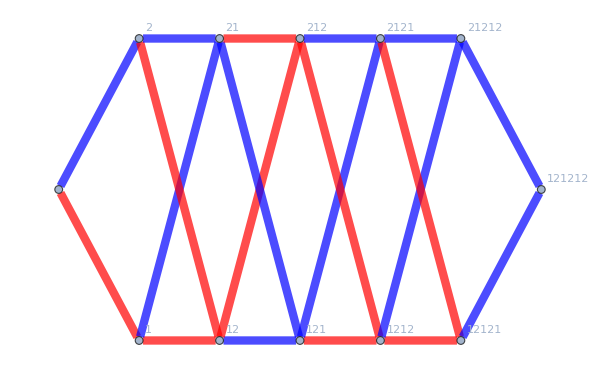

```mathematica
Graph[G,EdgeStyle->eLabels,ImageSize->600]
```

## Pretty display of complex with maps

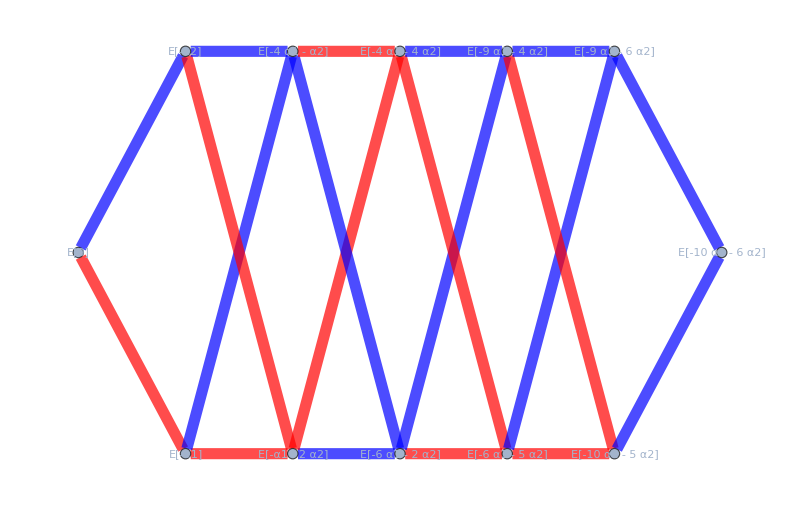

```mathematica
MakePretty[expression_]:=expression/.NonCommutativeMultiply[b__]:> StringJoin@(ToString[#,StandardForm]&/@{b});(*Make an expression involving NonCommutativeMultiply human readable.*)
edgeLabels = #[[1]]->Placed[#[[2]],Tooltip]&/@Normal@KeyMap[edgeAssocReverse,MakePretty/@edgeWeights]; (*Add a tooltip with the BGG Map
*)Graph[G,EdgeLabels->edgeLabels,VertexLabels->vertexNames,EdgeStyle->eLabels,ImageSize->800](*mouseover the edges to see the maps*)
```

## Constructing the BGG complex

### Definition of the Lie Algebra

We define the adjoint action by coding in all the Chevally-Serre relations on a basis {h_1,h_2,f_I,e_I} with I∈{1,2,12,112,1112,11122}. We use the convention that 
[f_I,f_J]=Sign[I*J] f_Sort[I*J] where I*J is the concatenation of I and J and Sign[I*J] is the sign of the permutation which sorts I*J.

For i,j ∈{1,2} we have [h_i,e_j]=A_ij e_j,[h_i,f_j]=-A_ij f_j with A_ij the Cartan matrix. This extends to
	[h_i,e_J]=(Σ_(j∈J)A_ij)e_J
	[h_i,f_J]=-(Σ_(j∈J)A_ij)f_J	

Finally we know that for i,j∈{1,2} we have [e_i,f_j]=δ_ij h_i. We can then apply the Jacobi identity in specific ways to compute [e_I,f_J].

Next we tell Mathematica that the Lie bracket is bilinear, and after we can test if it can compute all the brackets by computing all the structure constants and putting them in a table.

All of this should be easily generalized to an arbitrary Cartan matrix

```mathematica
Remove[ad]
CartanMatrix = {{2,-3},{-1,2}};
Cartan[i_,j_]:=Total[CartanMatrix[[i,#]]&/@IntegerDigits[j]]

G2Basis = {Subscript[f, 1],Subscript[f, 2],Subscript[f, 12],Subscript[f, 112],Subscript[f, 1112],Subscript[f, 11122],Subscript[e, 1],Subscript[e, 2],Subscript[e, 12],Subscript[e, 112],Subscript[e, 1112],Subscript[e, 11122],Subscript[h, 1],Subscript[h, 2]};
AllowedDigits = {1,2,12,112,1112,11122};

(*Concatenate and sort two indices and compute the signature of the permutation sorting the concatenation*)
ConcatDigits[i_,j_]:=Module[{DigitList,OutputDigit},
DigitList=Join[IntegerDigits[i],IntegerDigits[j]];
OutputDigit=FromDigits@Sort[DigitList];
If[MemberQ[AllowedDigits,OutputDigit],
Return[{OutputDigit,Signature[Ordering[DigitList]]}],
Return[{0,0}]
];
]
ad[Subscript[f, i_],Subscript[f, j_]]:=Subscript[f, #[[1]]]#[[2]]&@ConcatDigits[i,j]
ad[Subscript[e, i_],Subscript[e, j_]]:=Subscript[e, #[[1]]]#[[2]]&@ConcatDigits[i,j]

ad[Subscript[f, 1],Subscript[e, 1]]:=-Subscript[h, 1]
ad[Subscript[f, 1],Subscript[e, 2]]:=0
ad[Subscript[f, 2],Subscript[e, 1]]:=0
ad[Subscript[f, 2],Subscript[e, 2]]:=-Subscript[h, 2]

ad[Subscript[e, 1],Subscript[f, 1]]:=Subscript[h, 1]
ad[Subscript[e, 1],Subscript[f, 2]]:=0
ad[Subscript[e, 2],Subscript[f, 1]]:=0
ad[Subscript[e, 2],Subscript[f, 2]]:=Subscript[h, 2]

ad[Subscript[h, i_],Subscript[e, j_]]:=Cartan[i,j] Subscript[e, j]
ad[Subscript[e, i_],Subscript[h, j_]]:=-Cartan[j,i] Subscript[e, i]
ad[Subscript[h, i_],Subscript[f, j_]]:=-Cartan[i,j] Subscript[f, j]
ad[Subscript[f, i_],Subscript[h, j_]]:=Cartan[j,i] Subscript[f, i]

ad[Subscript[h, _],Subscript[h, _]]:=0

JacobiIdentityR = ad[x_,ad[y_,z_]]->ad[ad[x,y],z]+ad[y,ad[x,z]];
JacobiIdentityL = ad[ad[x_,y_],z_]->ad[ad[x,z],y]+ad[x,ad[y,z]];

ad[Subscript[f, i_],Subscript[e, 12]]:=ad[Subscript[f, i],ad[x,y]]/.JacobiIdentityR/.{x->Subscript[e, 1],y->Subscript[e, 2]}
ad[Subscript[f, i_],Subscript[e, 112]]:=ad[Subscript[f, i],ad[x,y]]/.JacobiIdentityR/.{x->Subscript[e, 1],y->Subscript[e, 12]}
ad[Subscript[f, i_],Subscript[e, 1112]]:=ad[Subscript[f, i],ad[x,y]]/.JacobiIdentityR/.{x->Subscript[e, 1],y->Subscript[e, 112]}
ad[Subscript[f, i_],Subscript[e, 11122]]:=-ad[Subscript[f, i],ad[x,y]]/.JacobiIdentityR/.{x->Subscript[e, 2],y->Subscript[e, 1112]}

ad[Subscript[e, 12],Subscript[f, i_]]:=ad[ad[x,y],Subscript[f, i]]/.JacobiIdentityL/.{x->Subscript[e, 1],y->Subscript[e, 2]}
ad[Subscript[e, 112],Subscript[f, i_]]:=ad[ad[x,y],Subscript[f, i]]/.JacobiIdentityL/.{x->Subscript[e, 1],y->Subscript[e, 12]}
ad[Subscript[e, 1112],Subscript[f, i_]]:=ad[ad[x,y],Subscript[f, i]]/.JacobiIdentityL/.{x->Subscript[e, 1],y->Subscript[e, 112]}
ad[Subscript[e, 11122],Subscript[f, i_]]:=-ad[ad[x,y],Subscript[f, i]]/.JacobiIdentityL/.{x->Subscript[e, 2],y->Subscript[e, 1112]}

ad[Subscript[f, 12],Subscript[e, i_]]:=ad[ad[x,y],Subscript[e, i]]/.JacobiIdentityL/.{x->Subscript[f, 1],y->Subscript[f, 2]}
ad[Subscript[f, 112],Subscript[e, i_]]:=ad[ad[x,y],Subscript[e, i]]/.JacobiIdentityL/.{x->Subscript[f, 1],y->Subscript[f, 12]}
ad[Subscript[f, 1112],Subscript[e, i_]]:=ad[ad[x,y],Subscript[e, i]]/.JacobiIdentityL/.{x->Subscript[f, 1],y->Subscript[f, 112]}
ad[Subscript[f, 11122],Subscript[e, i_]]:=-ad[ad[x,y],Subscript[e, i]]/.JacobiIdentityL/.{x->Subscript[f, 2],y->Subscript[f, 1112]}

ad[Subscript[e, i_],Subscript[f, 12]]:=ad[Subscript[e, i],ad[x,y]]/.JacobiIdentityR/.{x->Subscript[f, 1],y->Subscript[f, 2]}
ad[Subscript[e, i_],Subscript[f, 112]]:=ad[Subscript[e, i],ad[x,y]]/.JacobiIdentityR/.{x->Subscript[f, 1],y->Subscript[f, 12]}
ad[Subscript[e, i_],Subscript[f, 1112]]:=ad[Subscript[e, i],ad[x,y]]/.JacobiIdentityR/.{x->Subscript[f, 1],y->Subscript[f, 112]}
ad[Subscript[e, i_],Subscript[f, 11122]]:=-ad[Subscript[e, i],ad[x,y]]/.JacobiIdentityR/.{x->Subscript[f, 2],y->Subscript[f, 1112]}

ad[Plus[y1_+y2_],z_]:=ad[y1,z]+ad[y2,z]
ad[y_,Plus[z1_,z2_]]:=ad[y,z1]+ad[y,z2]
ad[x___,Times[λ_?NumberQ,y_],z___]:=λ ad[x,y,z]
ad[___,0,___]:=0

Labeled[TableForm[Outer[Expand@*ad,G2Basis,G2Basis],TableHeadings->{G2Basis,G2Basis},TableSpacing->{2, 2}],Style["Multiplication table of g2\n",22,Bold],Top]
```

| f_1 | f_2 | f_12 | f_112 | f_1112 | f_11122 | e_1 | e_2 | e_12 | e_112 | e_1112 | e_11122 | h_1 | h_2
f_1 | 0 | f_12 | f_112 | f_1112 | 0 | 0 | -h_1 | 0 | 3 e_2 | 4 e_12 | 3 e_112 | 0 | 2 f_1 | -f_1
f_2 | -f_12 | 0 | 0 | 0 | -f_11122 | 0 | 0 | -h_2 | -e_1 | 0 | 0 | -e_1112 | -3 f_2 | 2 f_2
f_12 | -f_112 | 0 | 0 | f_11122 | 0 | 0 | -3 f_2 | f_1 | h_1+3 h_2 | 4 e_1 | 0 | -3 e_112 | -f_12 | f_12
f_112 | -f_1112 | 0 | -f_11122 | 0 | 0 | 0 | -4 f_12 | 0 | -4 f_1 | -8 h_1-12 h_2 | -12 e_1 | -12 e_12 | f_112 | 0
f_1112 | 0 | f_11122 | 0 | 0 | 0 | 0 | -3 f_112 | 0 | 0 | 12 f_1 | 36 h_1+36 h_2 | -36 e_2 | 3 f_1112 | -f_1112
f_11122 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | f_1112 | 3 f_112 | 12 f_12 | 36 f_2 | -36 h_1-72 h_2 | 0 | f_11122
e_1 | h_1 | 0 | 3 f_2 | 4 f_12 | 3 f_112 | 0 | 0 | e_12 | e_112 | e_1112 | 0 | 0 | -2 e_1 | e_1
e_2 | 0 | h_2 | -f_1 | 0 | 0 | -f_1112 | -e_12 | 0 | 0 | 0 | -e_11122 | 0 | 3 e_2 | -2 e_2
e_12 | -3 e_2 | e_1 | -h_1-3 h_2 | 4 f_1 | 0 | -3 f_112 | -e_112 | 0 | 0 | e_11122 | 0 | 0 | e_12 | -e_12
e_112 | -4 e_12 | 0 | -4 e_1 | 8 h_1+12 h_2 | -12 f_1 | -12 f_12 | -e_1112 | 0 | -e_11122 | 0 | 0 | 0 | -e_112 | 0
e_1112 | -3 e_112 | 0 | 0 | 12 e_1 | -36 h_1-36 h_2 | -36 f_2 | 0 | e_11122 | 0 | 0 | 0 | 0 | -3 e_1112 | e_1112
e_11122 | 0 | e_1112 | 3 e_112 | 12 e_12 | 36 e_2 | 36 h_1+72 h_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e_11122
h_1 | -2 f_1 | 3 f_2 | f_12 | -f_112 | -3 f_1112 | 0 | 2 e_1 | -3 e_2 | -e_12 | e_112 | 3 e_1112 | 0 | 0 | 0
h_2 | f_1 | -2 f_2 | -f_12 | 0 | f_1112 | -f_11122 | -e_1 | 2 e_2 | e_12 | 0 | -e_1112 | e_11122 | 0 | 0Multiplication table of g2

### Definition of adjoint action

Next we define the adjoint action on g2, and on wedge products, tensor products, and symmetric products of elements of the Lie algebra to extend the adjoint action to arbitrary weight modules. 

First of all we will always act with a non-commutative power series in f_I for I∈{1,2,12,112,1112,11122}. The action is linear, and we define

ad((∏^n)_(k=1)(f_I_k)^d_k)(X) = (ad(f_I_n))^d_n(◦⋯◦ad(f_I_1))^d_1(X)

Then we define ad[x,y⊗z]=ad[x,y]⊗z+y⊗ad[x,z]. This extends to the tensor algebra, and also descends down to the exterior and symmetric algebra. 
Furthermore we make Mathematica collect terms in tensor/symmetric/wedge products by setting e.g. (a⊗b)⊗c→a⊗b⊗c=CircleTimes[a,b,c].
We also take multilinearity of tensor product into account by setting a⊗(b_1+λ b_2)⊗c =a⊗b_1⊗c+λ(a⊗b_2⊗c) .
Finally we make Mathematica sort the terms in a symmetric product, and wedge product. When sorting the terms in a wedge product we multiply by the sign of the permutation used to sort the terms. 
The tensor, wedge and symmetric product are compatible with each other, and there is no problem with for example defining (a⋀b)⊗c.

```mathematica
(*Fold[ad,z,List[x]] would give ad[...ad[ad[z,Subscript[x, 1]],Subscript[x, 2]],...,Subscript[x, n]], but we need ad[Subscript[x, n],...ad[Subscript[x, 2],ad[Subscript[x, 1],z]]...], and for this we essentially reverse the list x and reverse the arguments of ad[] every time.*)
adReverse[x_,y_]:=ad[y,x]
ad[NonCommutativeMultiply[x__],z_]:=Fold[adReverse,z,Reverse[List[x]]]
ad[Power[x_,n_],z_]:=ad[NonCommutativeMultiply@@ConstantArray[x,n],z]


WedgeRelations = {Wedge[___,0,___]->0,
Wedge[Wedge[c1__,c2__],c3__]->Wedge[c1,c2,c3],Wedge[c1__,Wedge[c2__,c3__]]->Wedge[c1,c2,c3],Wedge[c1___,Plus[c2_,c3_],c4___]->Wedge[c1,c2,c4]+Wedge[c1,c3,c4],
Wedge[c1___,Times[λ_?NumberQ,c2_],c3___]->λ Wedge[c1,c2,c3],
Wedge[a__]:>Signature[{a}]* Wedge@@Sort[{a}]
};

SymRelations = {CircleDot[___,0,___]->0,
CircleDot[CircleDot[c1__,c2__],c3__]->CircleDot[c1,c2,c3],CircleDot[c1__,CircleDot[c2__,c3__]]->CircleDot[c1,c2,c3],CircleDot[c1___,Plus[c2_,c3_],c4___]->CircleDot[c1,c2,c4]+CircleDot[c1,c3,c4],
CircleDot[c1___,Times[λ_?NumberQ,c2_],c3___]->λ CircleDot[c1,c2,c3],
CircleDot[a__]:>CircleDot@@Sort[{a}]
};

TensorRelations = {CircleTimes[___,0,___]->0,
CircleTimes[CircleTimes[c1__,c2__],c3__]->CircleTimes[c1,c2,c3],CircleTimes[c1__,CircleTimes[c2__,c3__]]->CircleTimes[c1,c2,c3],CircleTimes[c1___,Plus[c2_,c3_],c4___]->CircleTimes[c1,c2,c4]+CircleTimes[c1,c3,c4],
CircleTimes[c1___,Times[λ_?NumberQ,c2_],c3___]->λ CircleTimes[c1,c2,c3]
};
ModuleRelations = Join[WedgeRelations,SymRelations,TensorRelations];

ad[x_,Wedge[a_,b_]]:=(Wedge[ad[x,a],b]+Wedge[a,ad[x,b]])//.WedgeRelations
ad[x_,Wedge[a_,b_,c__]]:=(Wedge[ad[x,a],b,c]+Wedge[a,ad[x,Wedge[b,c]]])//.WedgeRelations

ad[x_,CircleTimes[a_,b_]]:=(CircleTimes[ad[x,a],b]+CircleTimes[a,ad[x,b]])//.TensorRelations
ad[x_,CircleTimes[a_,b_,c__]]:=(CircleTimes[ad[x,a],b,c]+CircleTimes[a,ad[x,CircleTimes[b,c]]])//.TensorRelations

ad[x_,CircleDot[a_,b_]]:=(CircleDot[ad[x,a],b]+CircleDot[a,ad[x,b]])//.SymRelations
ad[x_,CircleDot[a_,b_,c__]]:=(CircleDot[ad[x,a],b,c]+CircleDot[a,ad[x,CircleDot[b,c]]])//.SymRelations
```

### Definition of coadjoint action

The Lie algebra splits as g=n⊕h⊕u=b⊕u, respectively spanned by f_I,h_i,e_I. This splitting defines a pairing on g by ⟨e_I,f_J⟩=δ_IJ, ⟨h_i,h_j⟩=δ_ij and otherwise zero, and extending by bilinearity and symmetry. This pairing is non-degenerate and identifies n,u as each other’s dual, and h is self-dual. 
The coadjoint action is then defined by ⟨(ad^*ξ)X,Y⟩=-⟨X,ad(ξ)Y⟩. In practice this means that
	ad^*(ξ)X = -∑_α ⟨X,[ξ,α]⟩α^*
where α runs over a the Chevallay basis of g and α^* is the dual basis element under the pairing. 

We are actually only interested in the coadjoint action restricted to a map b⊗u→u. In practice this map takes form
	ad(|_u)^*(ξ)X = -∑_I ⟨X,[ξ,f_I]⟩e_I

We also define the map ϕ: b→n⊗u by ϕ(X)=∑_I f_I⊗(ad(|_u)^*(X)(e_I))

We need an action of n on n,u,b,g. This action is defined as the adjoint action on n,b,g  but as the (restricted) coadjoint action on u. For practical reasons we denote any element of (a symmetric power) of u not by e_I but by e'_I, and then define ad(X)(e'_I)=ad(|_u)^*(X)(e'_I).

Finally we compute the multiplication table of the (restricted) coadjoint action.

```mathematica
Remove[InnerProduct]
InnerProduct[x___,Times[λ_?NumberQ ,y_],z___]:=λ InnerProduct[x,y,z]
InnerProduct[x___,Plus[y1_,y2_],z___]:=InnerProduct[x,y1,z]+InnerProduct[x,y2,z]
InnerProduct[Subscript[e, i_],Subscript[f, j_]]:=KroneckerDelta[i,j]
InnerProduct[Subscript[f, i_],Subscript[e, j_]]:=KroneckerDelta[i,j]
InnerProduct[Subscript[e, _],Subscript[e, _]]:=0
InnerProduct[Subscript[f, _],Subscript[f, _]]:=0
InnerProduct[Subscript[h, i_],Subscript[h, j_]]:=KroneckerDelta[i,j]
InnerProduct[Subscript[h, _],Subscript[e, _]]:=0
InnerProduct[Subscript[h, _],Subscript[f, _]]:=0
InnerProduct[Subscript[e, _],Subscript[h, _]]:=0
InnerProduct[Subscript[f, _],Subscript[h, _]]:=0
InnerProduct[___,0,___]:=0
InnerProduct[x___,Subscript[e', i_],y___]:=InnerProduct[x,Subscript[e, i],y]

Dual[Subscript[e, i_]]:=Subscript[f, i]
Dual[Subscript[f, i_]]:=Subscript[e, i]
Dual[Subscript[h, i_]]:=Subscript[h, i]


coad[x_,y_]:=-Total[InnerProduct[y,ad[x,#]]Dual[#]&/@G2Basis]
rcoad[x_,y_]:=-Total[InnerProduct[y,ad[x,Subscript[f, #]]] Subscript[e', #]&/@AllowedDigits]
ϕ[x_]:=Total[CircleTimes[Subscript[f, #],rcoad[x,Subscript[e', #]]]//.TensorRelations&/@AllowedDigits]
ad[x_,Subscript[e', i_]]:=rcoad[x,Subscript[e', i]]
```

```mathematica
(*TableForm[Outer[Expand@*coad,G2Basis,G2Basis],TableHeadings->{G2Basis,G2Basis},TableSpacing->{2, 2}]*)
Labeled[TableForm[Outer[Expand@*rcoad,G2Basis,G2Basis],TableHeadings->{G2Basis,G2Basis},TableSpacing->{2, 2}],Style["Multiplication table of restricted coadjoint action on g2\n",22,Bold],Top]
```

| f_1 | f_2 | f_12 | f_112 | f_1112 | f_11122 | e_1 | e_2 | e_12 | e_112 | e_1112 | e_11122 | h_1 | h_2
f_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e'_2 | -e'_12 | -e'_112 | 0 | 0 | 0
f_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e'_1 | 0 | 0 | e'_1112 | 0 | 0
f_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e'_1 | 0 | -e'_112 | 0 | 0
f_112 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e'_1 | e'_12 | 0 | 0
f_1112 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e'_2 | 0 | 0
f_11122 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 e'_12 | -4 e'_112 | -3 e'_1112 | 0 | 0 | -e'_1 | 0
e_2 | 0 | 0 | 0 | 0 | 0 | 0 | e'_12 | 0 | 0 | 0 | e'_11122 | 0 | 0 | -e'_2
e_12 | -e'_2 | 3 e'_1 | 0 | 0 | 0 | 0 | -4 e'_112 | 0 | 0 | 3 e'_11122 | 0 | 0 | e'_12 | 3 e'_12
e_112 | 4 e'_12 | 0 | 4 e'_1 | 0 | 0 | 0 | 12 e'_1112 | 0 | 12 e'_11122 | 0 | 0 | 0 | -8 e'_112 | -12 e'_112
e_1112 | -12 e'_112 | 0 | 0 | 3 e'_1 | 0 | 0 | 0 | 36 e'_11122 | 0 | 0 | 0 | 0 | 36 e'_1112 | 36 e'_1112
e_11122 | 0 | -36 e'_1112 | -12 e'_112 | -3 e'_12 | -e'_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -36 e'_11122 | -72 e'_11122
h_1 | 0 | 0 | 0 | 0 | 0 | 0 | 2 e'_1 | -3 e'_2 | -e'_12 | e'_112 | 3 e'_1112 | 0 | 0 | 0
h_2 | 0 | 0 | 0 | 0 | 0 | 0 | -e'_1 | 2 e'_2 | e'_12 | 0 | -e'_1112 | e'_11122 | 0 | 0Multiplication table of restricted coadjoint action on g2

### Tools for constructing weight modules.

All the elements of g have a well-defined weight w∈Z×Z. 
	w(h_i)=(0,0)
	w(e_I)=(a,b), where a is the number of 1’s in I and b  the number of 2’s in I.
	w(f_I)=(-a,-b). 
The weight satisfies w(x⊗y)=w(x)+w(y), same for wedge and symmetric products. Changing an element by a scalar, does not affect it’s weight so we throw away all the scalars when computing weight. 
We only really compute the weight of things which are a priori homogeneous (wrt. weight), so when we compute the weight we simply say w(x+y)=w(x).

We want to compute bases of modules of form direct sums of spaces of form S^i(u)⊗⋀^j g⊗⋀^k n. To do this we define tensor/wedge/symmetric products of lists, e.g.
	{a,b,c}⊗{d,e} = {a⊗d,a⊗e,b⊗d,b⊗e,c⊗d,c⊗e}
and for symmetric/wedge products we also sort all the terms, and remove all the duplicates. For wedge product we also remove all the zero terms, which appear if a term occurs twice in a single product.  For consistency it only computes this if all the arguments of ⊗,⋀,⊙,⊕ are lists. This is important because these operations do not commute with each other. 

We feed Mathematica strings like “(u⊙u)⊗g⊗(n⋀n)”. Mathematica then substitutes u,g,n for a list containing their respective bases, and then computes the tensor/wedge/symmetric product of these lists as outlined below. When we see a direct sum ⊕ we just concatenate the two lists.

```mathematica
nbasis = Subscript[f,#]&/@AllowedDigits
bbasis = Join[{Subscript[h, 1],Subscript[h, 2]},nbasis]
ubasis = Subscript[e',#]&/@AllowedDigits
gbasis = Join[bbasis,ubasis]/.e'->e


Weight[Subscript[f, i_]]:=-{Count[#,1],Count[#,2]}&@IntegerDigits[i]
Weight[Subscript[e, i_]]:={Count[#,1],Count[#,2]}&@IntegerDigits[i]
Weight[Subscript[e', i_]]:={Count[#,1],Count[#,2]}&@IntegerDigits[i]
Weight[Subscript[h, _]]:={0,0}
Weight[Plus[a_,b_]]:=Weight[a]
Weight[CircleTimes[a__]]:=Weight[a]
Weight[Wedge[a__]]:=Weight[a]
Weight[CircleDot[a__]]:=Weight[a]
Weight[a_,b__]:=Weight[a]+Weight[b]
Weight[Times[_?NumberQ,a_]]:=Weight[a]

BasisDict =<|"g"->gbasis,"u"->ubasis,"b"->bbasis,"n"->nbasis,"phi0"->{phi[0]},"phi1"->{phi[1]},"phi2"->{phi[2]}|>;
GeneratorWedgeSimplify[x_]:=DeleteCases[DeleteDuplicates[(x/.WedgeRelations/.Times[_?NumberQ,b_]:>b)],0]
GeneratorSymSimplify[x_]:=DeleteCases[DeleteDuplicates[(x/.SymRelations/.Times[_?NumberQ,b_]:>b)],0]
TensorWedgeToList[l_]:=l//.{
Wedge[a__?ListQ]:>GeneratorWedgeSimplify[Wedge@@@Tuples[{a}]],
CircleTimes[a__?ListQ]:>DeleteDuplicates[CircleTimes@@@Tuples[{a}]],
CircleDot[a__?ListQ]:>GeneratorSymSimplify[CircleDot@@@Tuples[{a}]]
}//GeneratorWedgeSimplify//GeneratorSymSimplify
```

{f_1,f_2,f_12,f_112,f_1112,f_11122}

{h_1,h_2,f_1,f_2,f_12,f_112,f_1112,f_11122}

{e'_1,e'_2,e'_12,e'_112,e'_1112,e'_11122}

{h_1,h_2,f_1,f_2,f_12,f_112,f_1112,f_11122,e_1,e_2,e_12,e_112,e_1112,e_11122}

## Computing cohomology

### Defining the modules

We fix some even 0≤b≤a≤12, and define i,j by a=i+j, b=j-i and set k=-a. We then define 
	M_j^k=(⊕_(r=0))^(j+k/2)(⊙^(j+k/2-r)u)⊗(⋀^r g)⊗(⋀^(j+k/2) n)
Essentially we define the degree of u,g,n to be resp. 2,0,-2, and we wish to find the modules with degree k. 
Later we then extract the weight λ part M_j^k[λ]. 

We then also have a submodule T_j^k→M_j^k (respecting weight grading). It is defined by map R: b→g⊕u⊗n, sending x:>(x,ϕ(x)). More precisely, T_j^k is the image of the inclusion R(b)⊗(M_(j-1))^k→M_j^k. The implementation of this was a little finicky, and hacky.

Finally we will work with the module E_j^k defined as the quotient T_j^k→M_j^k→E_j^k.

```mathematica
WedgePower[x_,1]:=x
WedgePower[x_,0]:="1"
WedgePower[x_,n_?IntegerQ]:=Wedge@@ConstantArray[x,n]
SymPower[x_,1]:=x
SymPower[x_,0]:="1"
SymPower[x_,n_?IntegerQ]:=CircleDot@@ConstantArray[x,n]
ModuleTensorSimplifyRelations ={CircleTimes[c1___,"1",c2___]:>CircleTimes[c1,c2],CircleTimes[x_]:> x,Wedge[c1___,"1",c2___]:>Wedge[c1,c2],Wedge[x_]:> x,CircleDot[c1___,"1",c2___]:>CircleDot[c1,c2],CircleDot[x_]:> x,
CircleDot[c1___,CircleDot[c2__],c3___]->CircleDot[c1,c2,c3],
CircleTimes[c1___,CircleTimes[c2__],c3___]->CircleTimes[c1,c2,c3],
Wedge[c1___,Wedge[c2__],c3___]->Wedge[c1,c2,c3]}
```

{c1___⊗1⊗c2___:>c1⊗c2,⊗x_:>x,c1___⋀1⋀c2___:>c1⋀c2,Wedge[x_]:>x,c1___⊙1⊙c2___:>c1⊙c2,CircleDot[x_]:>x,c1___⊙CircleDot[c2__]⊙c3___→c1⊙c2⊙c3,c1___⊗⊗c2__⊗c3___→c1⊗c2⊗c3,c1___⋀Wedge[c2__]⋀c3___→c1⋀c2⋀c3}

```mathematica
M[j_,k_]:=Table[SymPower["u",j+k/2-r]⊗WedgePower["g",r]⊗WedgePower["n",j-r],{r,0,j+k/2}]//.ModuleTensorSimplifyRelations
MBasis [j_,k_]:=DeleteDuplicates@(Join@@(M[j,k]/.BasisDict//TensorWedgeToList))
```

```mathematica
TRaw[j_,k_]:=Table[(SymPower["u",j+k/2-r]⊙"phi1")⊗("phi0"⋀WedgePower["g",r])⊗(WedgePower["n",j-r]⋀"phi2"),{r,0,j+k/2}]//.ModuleTensorSimplifyRelations
R[x_]:={phi[0]->x,({phi[1]->(#[[2]]),phi[2]->(#[[1]]/.Times[λ_?NumberQ,y_]:>y)}&/@DeleteCases[(ϕ[x]+CircleTimes[{0,0}]/.{Plus->List,CircleTimes->List}),{{0,0}}])}
RImage=R/@bbasis
GetPhiImage[x_]:=((x[[1]]/.#[[1]])+Total[x[[2]]/.#[[2]]])//.Join[TensorRelations,WedgeRelations,SymRelations] &/@RImage
PhiRelations[j_,k_]:=((({#/.{phi[1]->"1",phi[2]->"1"},#/.phi[0]->"1"})//.ModuleTensorSimplifyRelations&)/@Join@@(TRaw[j-1,k]/.BasisDict//TensorWedgeToList))
TBasis[j_,k_]:=DeleteDuplicates[Join@@(GetPhiImage/@PhiRelations[j,k])]
```

{{phi[0]→h_1,{{phi[1]→2 e'_1,phi[2]→f_1},{phi[1]→-3 e'_2,phi[2]→f_2},{phi[1]→-e'_12,phi[2]→f_12},{phi[1]→e'_112,phi[2]→f_112},{phi[1]→3 e'_1112,phi[2]→f_1112}}},{phi[0]→h_2,{{phi[1]→-e'_1,phi[2]→f_1},{phi[1]→2 e'_2,phi[2]→f_2},{phi[1]→e'_12,phi[2]→f_12},{phi[1]→-e'_1112,phi[2]→f_1112},{phi[1]→e'_11122,phi[2]→f_11122}}},{phi[0]→f_1,{{phi[1]→-e'_2,phi[2]→f_12},{phi[1]→-e'_12,phi[2]→f_112},{phi[1]→-e'_112,phi[2]→f_1112}}},{phi[0]→f_2,{{phi[1]→e'_1,phi[2]→f_12},{phi[1]→e'_1112,phi[2]→f_11122}}},{phi[0]→f_12,{{phi[1]→e'_1,phi[2]→f_112},{phi[1]→-e'_112,phi[2]→f_11122}}},{phi[0]→f_112,{{phi[1]→e'_1,phi[2]→f_1112},{phi[1]→e'_12,phi[2]→f_11122}}},{phi[0]→f_1112,{{phi[1]→-e'_2,phi[2]→f_11122}}},{phi[0]→f_11122,{{phi[1]→0,phi[2]→0}}}}

### All the different a and b

```mathematica
Table[{2a,2b},{a,0,6},{b,0,Min[a,6-a]}]//TableForm
```

0
0 |  |  | 
2
0 | 2
2 |  | 
4
0 | 4
2 | 4
4 | 
6
0 | 6
2 | 6
4 | 6
6
8
0 | 8
2 | 8
4 | 
10
0 | 10
2 |  | 
12
0 |  |  |

### Computing cohomology

```mathematica
a=6;b=6;
i=(a-b)/2
j=(a+b)/2 
k=-a; 
Mjk = MBasis[j,k];
Tjk = TBasis[j,k];
```

0

6

```mathematica
M[j,k]
```

{u⊙u⊙u⊗n⋀n⋀n⋀n⋀n⋀n,u⊙u⊗g⊗n⋀n⋀n⋀n⋀n,u⊗g⋀g⊗n⋀n⋀n⋀n,g⋀g⋀g⊗n⋀n⋀n}

The cohomology is now computed as follows. First we define maps which select the roots of the ith column of the BGG complex, and compute their weights W_i. 
Then we compute a basis for M_j^k, and define a map which selects the parts of weights W_i. 
Next we retrieve the maps of the BGG complex together with their signs starting at the ith column and going to i+1st column. 
We have monomials generating M_j^k[W_i], but now we make an association turning these monomials into vectors to treat M_j^k[W_i] as vector space. 
Then in this basis we compute the action of the BGG maps on the basis, and get a matrix. We do this for i and i-1 and confirm that this map squares to 0.

We then compute a section E_j^k→M_j^k by picking a basis of T_j^k, adding to it the basis of M_j^k, row reducing, and then picking the bottom right part of the result. Previously we computed this section by first using Gram-Schmidt to compute a projection to T, but this is computationally extremely inefficient. 

Finally we precompose the differential on M_j^k with this section from E to M, and then apply the transpose of the section of E to M to it to project back to E. This is the differential on E. We compute the dimension of the kernel of the ith differential, and the dimension of image of the i-1-th, and subtract to obtain the cohomology.

```mathematica
BGGColumn[i_]:=Select[W,StringLength[#]==i&]
BGGWeights[i_]:=getAction/@BGGColumn[i]
FindWeightModule[weight_]:=Select[Mjk,Weight[#]==weight&]
BGGModule[i_]:=Flatten[{#->FindWeightModule[getAction[#]]}&/@BGGColumn[i],1]
BGGArrows[i_]:=Select[Keys[edgeAssoc],MemberQ[BGGColumn[i],#[[1]]]&];
BGGMaps[i_]:=Module[{maps},
maps={#[[1]],(#/.edgeAssoc/.edgeWeights)*(signs[[#/.edgeAssoc]])}&/@BGGArrows[i];
{#[[1,1]]->Total@#[[All,2]]}&/@GatherBy[maps,First]//Flatten
]
BasisRep[basis_]:=Join[{0->ConstantArray[0,Length[basis]]},Table[basis[[i]]->UnitVector[Length[basis],i],{i,Length[basis]}]]
BGGBassis[i_]:=BasisRep@Flatten@Values@BGGModule[i]
GetImage[i_,weight_]:=(ad[weight/.BGGMaps[i],#]&/@(weight/.BGGModule[i]))//.ModuleRelations/.BGGBassis[i+1]
```

```mathematica
BGGMatrix[i_]:=Flatten[GetImage[i,#]&/@BGGColumn[i],1]
BGGRelations[i_]:=Select[Tjk,MemberQ[BGGWeights[i],Weight[#]]&]/.BGGBassis[i]
BGGMDimension[i_]:=Length@Flatten@Values@BGGModule[i]

BGGMDimension/@{i-1,i,i+1}
```

{0,190,441}

```mathematica
BGGMatrix[i-1]//TensorDimensions
BGGMatrix[i]//TensorDimensions

If[BGGMDimension[i-1]>0,
Norm[Norm/@(BGGMatrix[i-1].BGGMatrix[i])],
0
]
```

{0}

{190,441}

```mathematica
ProjectToE[i_,Numeric_:False]:=Module[{orthoBasis,pT,basis},
orthoBasis=Orthogonalize[
If[Numeric,N[BGGRelations[i]],BGGRelations[i]]
];
pT[v_]:=Total[Dot[#,v]#&/@orthoBasis];
basis=UnitVector[BGGMDimension[i],#]&/@Range[BGGMDimension[i]];
Return[#-pT[#]&/@basis]
]
SectionFromE[i_,Numeric_:False]:=DeleteCases[Orthogonalize[ProjectToE[i,Numeric]],{0|0.,0...|0. ...,0|0.}]
```

```mathematica
FastESection[i_]:=Module[{relations,nRelations,dim},
dim = BGGMDimension[i];
If[dim==0,Return[{}]];

relations = BGGRelations[i];
nRelations=MatrixRank[relations/.{}->{{0}}];

If[nRelations==0,Return[IdentityMatrix[dim]]];
(Join[relations,IdentityMatrix[dim]]//Transpose//RowReduce)[[nRelations+1;;,Length[relations]+1;;]]
]
```

```mathematica
(*BGGDifferential[i_,Numeric_:False]:=SectionFromE[i,Numeric].If[Numeric,N[BGGMatrix[i]],BGGMatrix[i]].Transpose[SectionFromE[i+1,Numeric]]/.{Dot[0,_]->{{0}}};*)
BGGDifferential[i_]:=FastESection[i].BGGMatrix[i].Transpose[FastESection[i+1]]/.{Dot[0,_]->{{0}}};
```

```mathematica
KernelDimension = (BGGMDimension[i]-MatrixRank[BGGRelations[i]/.{}->{{}}])-MatrixRank[BGGDifferential[i]]
ImageDimenstion = MatrixRank[BGGDifferential[i-1]]
CohomologyDimension = KernelDimension-ImageDimenstion
```

1

0

1